```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210224_impacts_in_time_windows"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
data=Import["../data/ccm_manipulated_396096_partitioned_in_time_windows.mx",HeaderLines->1];
```

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[9,15,10];]
```

{217.313,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep[[1]][[i]],widthdataintimewindowsFixedstep[[2]][[i]],2,7,400,Green],{i,Range@10}];
```

```mathematica
singlerandomgraphs=Table[RandomGraph[{VertexCount[network],EdgeCount[network]}],{network,graphsandnodenumbers[[All,1]]}];
```

```mathematica
randomgraphs=RandomGraph[{VertexCount[graphsandnodenumbers[[1,1]]],EdgeCount[graphsandnodenumbers[[1,1]]]},1000];
```

```mathematica
Dimensions@randomgraphs
```

{1000}

```mathematica
RndmMumodularity = Mean[Table[GirwanNewmanmodularity[randomgraphs[[i]]],{i,1000}]];
```

```mathematica
RndSigmamodularity =StandardDeviation[Table[GirwanNewmanmodularity[randomgraphs[[i]]],{i,1000}]];
```

```mathematica
Xmodularityvalues=GirwanNewmanmodularity[graphsandnodenumbers[[1,1]]];
```

```mathematica
XWolfmodularityvalues=N@GraphAssortativity[graphsandnodenumbers[[1,1]],FindGraphCommunities[graphsandnodenumbers[[1,1]]],"Normalized"->False];
```

```mathematica
ZScore=Table[(i-RndmMumodularity)/RndSigmamodularity,{i,{Xmodularityvalues,XWolfmodularityvalues}}];
```

```mathematica
ZScore
```

{20.0324,20.6561}

modularity function

```mathematica
GirwanNewmanmodularity[xx_]:=Module[{network,m,Aij,B,u,β,s,Q,div1,div2,moditer,r1,r11,r12,r2,r21,r22,subfinal1Q,subfinal2Q,finalQ},
network=xx;
m=EdgeCount@network;
Aij=AdjacencyMatrix@network;
B=N@(Aij-Outer[Times,VertexDegree@network,VertexDegree@network]/(2*m));
u=Eigenvectors@B;
β=Eigenvalues@B;
s=(u/.x_/;x<0->-1)/.x_/;x≥0->1;
Q=(Total@(Table[(u[[i]].Flatten@s[[Flatten@Position[β,Max@β][[1]]]])^2,{i,VertexList@network}]*β))/(4*m);
div1=Flatten@Position[Flatten@s[[Flatten@Position[β,Max@β][[1]]]],_?Negative];
div2=Flatten@Position[Flatten@s[[Flatten@Position[β,Max@β][[1]]]],_?Positive];
moditer[pos_,B1_]:=Module[{Bg,ug,βg,sg,deltaQ,divv1,divv2,Bg1,Bg2},
Bg=(Table[B1[[i,j]]-KroneckerDelta[i,j]*Total@B1[[i,pos]],{i,Length@B1},{j,Length@B1}])[[pos,pos]];
ug=Eigenvectors@Bg;
βg=Eigenvalues@Bg;
sg=(ug/.x_/;x<0->-1)/.x_/;x≥0->1;
deltaQ=(Total@(Table[(ug[[i]].Flatten@sg[[Flatten@Position[βg,Max@βg][[1]]]])^2,{i,Range@Length@pos}]*βg))/(4*m);
divv1=Flatten@Position[Flatten@sg[[Flatten@Position[βg,Max@βg][[1]]]],_?Negative];
divv2=Flatten@Position[Flatten@sg[[Flatten@Position[βg,Max@βg][[1]]]],_?Positive];{deltaQ,divv1,divv2,Bg}];
r1=moditer[div1,B];
r11=If[r1[[1]]>0.001,moditer[r1[[2]],r1[[4]]],{0,0,0,0}];
r12=If[r1[[1]]>0.001,moditer[r1[[3]],r1[[4]]],{0,0,0,0}];
r2=moditer[div2,B];
r21=If[r2[[1]]>0.001,moditer[r2[[2]],r2[[4]]],{0,0,0,0}];
r22=If[r2[[1]]>0.001,moditer[r2[[3]],r2[[4]]],{0,0,0,0}];
subfinal1Q=If[r1[[1]]>0.001,If[r11[[1]]>0.001,If[r12[[1]]>0.001,r12[[1]]+r11[[1]]+r1[[1]],r11[[1]]+r1[[1]]],If[r12[[1]]>0.001,r12[[1]]+r1[[1]],r1[[1]]]],0];
subfinal2Q=If[r2[[1]]>0.001,If[r21[[1]]>0.001,If[r22[[1]]>0.001,r22[[1]]+r21[[1]]+r2[[1]],r21[[1]]+r2[[1]]],If[r22[[1]]>0.001,r22[[1]]+r2[[1]],r2[[1]]]],0];
finalQ=Q+subfinal1Q+subfinal2Q]
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomGNmodularityvalues=Table[GirwanNewmanmodularity[singlerandomgraphs[[i]]],{i,Length@singlerandomgraphs}];
```

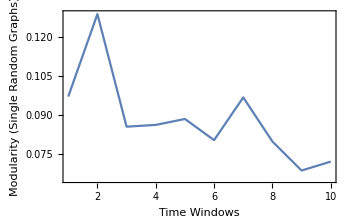

```mathematica
ListLinePlot[Thread[{Range@10,singlerandomGNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All}]
```

```mathematica
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]
```

The currently installed versions of IGraph/M are: {}

Installing IGraph/M is complete: PacletObject[…].

It can now be loaded using the command <<IGraphM`

```mathematica
<<"IGraphM`"
```

IGraph/M 0.5.1 (October 12, 2020)
Evaluate IGDocumentation[] to get started.

```mathematica
IGDegreeSequenceGame[Total[mat],Method->"VigerLatapy"]
```

```mathematica
list={};
```

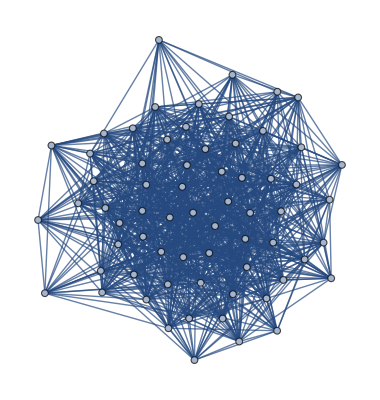
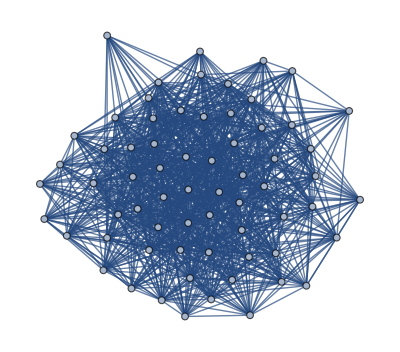

```mathematica
Table[IGDegreeSequenceGame[Total[AdjacencyMatrix@graphsandnodenumbers[[9]][[1]]],Method->"VigerLatapy"],{i,1000}]
```

```mathematica
%36[[1]]==%36[[2]]
```

False

```mathematica
Table[2+2,{i,3}]
```

{4,4,4}

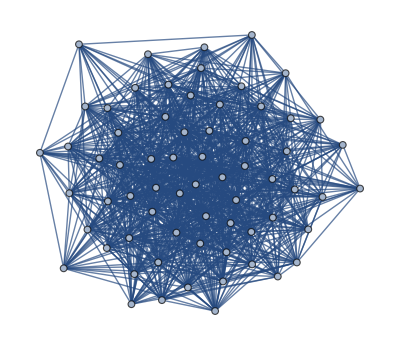

```mathematica
%12
```